```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab9\lab9\lab9

```mathematica
num = Import["test3.txt","Table"]
```

{{0,0.01,0.04,0.09,0.16,0.25,0.36,0.49,0.64,0.81,1},{0.00999693,0.0199972,0.0499973,0.0999973,0.169997,0.259997,0.369997,0.499997,0.649997,0.819997,1.01},{0.0399942,0.0499946,0.0799948,0.129995,0.199995,0.289995,0.399995,0.529995,0.679995,0.849995,1.03999},{0.089992,0.0999926,0.129993,0.179993,0.249993,0.339993,0.449993,0.579993,0.729993,0.899993,1.08999},{0.159991,0.169991,0.199992,0.249992,0.319992,0.409992,0.519992,0.649992,0.799992,0.969991,1.15999},{0.24999,0.259991,0.289991,0.339991,0.409991,0.499992,0.609991,0.739991,0.889991,1.05999,1.24999},{0.359991,0.369991,0.399992,0.449992,0.519992,0.609992,0.719992,0.849992,0.999992,1.16999,1.35999},{0.489992,0.499993,0.529993,0.579993,0.649993,0.739993,0.849993,0.979993,1.12999,1.29999,1.48999},{0.639994,0.649995,0.679995,0.729995,0.799995,0.889995,0.999995,1.12999,1.27999,1.44999,1.63999},{0.809997,0.819997,0.849997,0.899997,0.969997,1.06,1.17,1.3,1.45,1.62,1.81},{1,1.01,1.04,1.09,1.16,1.25,1.36,1.49,1.64,1.81,2}}

```mathematica
true = Table[(i*0.1)^2+(j*0.1)^2,{i,0,1/0.1},{j,0,1/0.1}] //Transpose
```

{{0.,0.01,0.04,0.09,0.16,0.25,0.36,0.49,0.64,0.81,1.},{0.01,0.02,0.05,0.1,0.17,0.26,0.37,0.5,0.65,0.82,1.01},{0.04,0.05,0.08,0.13,0.2,0.29,0.4,0.53,0.68,0.85,1.04},{0.09,0.1,0.13,0.18,0.25,0.34,0.45,0.58,0.73,0.9,1.09},{0.16,0.17,0.2,0.25,0.32,0.41,0.52,0.65,0.8,0.97,1.16},{0.25,0.26,0.29,0.34,0.41,0.5,0.61,0.74,0.89,1.06,1.25},{0.36,0.37,0.4,0.45,0.52,0.61,0.72,0.85,1.,1.17,1.36},{0.49,0.5,0.53,0.58,0.65,0.74,0.85,0.98,1.13,1.3,1.49},{0.64,0.65,0.68,0.73,0.8,0.89,1.,1.13,1.28,1.45,1.64},{0.81,0.82,0.85,0.9,0.97,1.06,1.17,1.3,1.45,1.62,1.81},{1.,1.01,1.04,1.09,1.16,1.25,1.36,1.49,1.64,1.81,2.}}

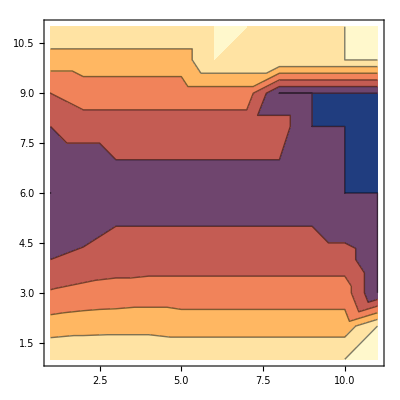

```mathematica
ListContourPlot[num-true]
```

```mathematica
g = Show[ListPlot3D[num,PlotRange->{{1,10},{1,10},{0.9,2.01}},PlotLegends->{{ "Численное решение"}}],ListPlot3D[true,PlotStyle->Blue,PlotLegends->{{ "Истинное решение"}}],ImageSize->600]
```

-Graphics3D-

```mathematica
ListContourPlot3D[true]
```

Visualization`Core`ListContourPlot3D::gmat1: Data value {{0.,0.01,0.04,0.09,0.16,0.25,0.36,0.49,0.64,0.81,«1»},{0.01,0.02,0.05,0.1,0.17,0.26,0.37,0.5,0.65,0.82,«1»},«7»,{0.81,0.82,0.85,0.9,0.97,1.06,1.17,1.3,1.45,1.62,«1»},«1»} must be a list of points of dimension 3.

ListContourPlot3D[{{0.,0.01,0.04,0.09,0.16,0.25,0.36,0.49,0.64,0.81,1.},{0.01,0.02,0.05,0.1,0.17,0.26,0.37,0.5,0.65,0.82,1.01},{0.04,0.05,0.08,0.13,0.2,0.29,0.4,0.53,0.68,0.85,1.04},{0.09,0.1,0.13,0.18,0.25,0.34,0.45,0.58,0.73,0.9,1.09},{0.16,0.17,0.2,0.25,0.32,0.41,0.52,0.65,0.8,0.97,1.16},{0.25,0.26,0.29,0.34,0.41,0.5,0.61,0.74,0.89,1.06,1.25},{0.36,0.37,0.4,0.45,0.52,0.61,0.72,0.85,1.,1.17,1.36},{0.49,0.5,0.53,0.58,0.65,0.74,0.85,0.98,1.13,1.3,1.49},{0.64,0.65,0.68,0.73,0.8,0.89,1.,1.13,1.28,1.45,1.64},{0.81,0.82,0.85,0.9,0.97,1.06,1.17,1.3,1.45,1.62,1.81},{1.,1.01,1.04,1.09,1.16,1.25,1.36,1.49,1.64,1.81,2.}}]

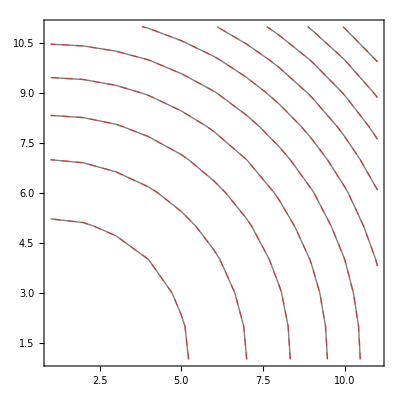

```mathematica
g=Show[ListContourPlot[num,ContourShading->None,Contours->10],ListContourPlot[true,ContourShading->None,ContourStyle->Directive[{Red,Dashed}],Contours->10]]
```

```mathematica
Export["test3.png",g]
```

test3.png